### Start choosing the example:

```mathematica
t=15;
beta = 0;
A =0.2;
g[x]
```

Log[x]

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,0,0},{1,0,0},{1,0,0}},Entrance Vertices and Currents→{{2,I1},{3,I2}},Exit Vertices and Terminal Costs→{{1,U1}},Switching Costs→{{2,1,3,S1},{3,1,2,S2}}|>

```mathematica
MFGEquations["uvars"]
```

<|{1,1->ex6175}→u6196,{2,2->1}→u6197,{3,3->1}→u6198,{en6173,en6173->2}→u6199,{en6174,en6174->3}→u6200,{ex6175,1->ex6175}→u6201,{1,2->1}→u6202,{1,3->1}→u6203,{2,en6173->2}→u6204,{3,en6174->3}→u6205|>

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: The system is:
True
and the rules are:
<|j6179→1,j6180→1,u6201→0,j6176→2,j6177→1,j6178→1,j6181→0,j6182→0,j6183→0,j6184→0,j6185→0,jt6186→0,jt6187→0,jt6188→1,jt6189→0,jt6190→1,jt6191→0,jt6192→0,jt6193→1,jt6194→0,jt6195→1,u6196→0,u6202→-1+1,u6203→-1+1,u6204→1,u6205→1,u6197→1,u6198→1,u6199→1,u6200→1|>

DataToEquations: It took 2.×10^-6 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.011752,Null}

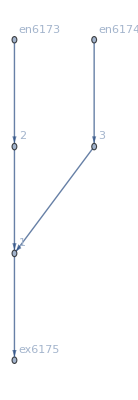

<|j6176→2,j6177→1,j6178→1,j6179→1,j6180→1,j6181→0,j6182→0,j6183→0,j6184→0,j6185→0,jt6186→0,jt6187→0,jt6188→1,jt6189→0,jt6190→1,jt6191→0,jt6192→0,jt6193→1,jt6194→0,jt6195→1,u6196→0,u6197→1,u6198→1,u6199→1,u6200→1,u6201→0,u6202→0,u6203→0,u6204→1,u6205→1|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->1,I2->1,U1->0,S1->27,S2->0}];//Timing
MFGEquations["FG"]
MFGEquations["criticalreduced1"][[2]]//KeySort
```

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.20736×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.20736×10^-17

<|j2775→110.,j2776→80.,j2777→30.,j2778→80.,j2779→30.,j2780→0.,j2781→0.,j2782→0.,j2783→0.,j2784→0.,jt2785→0.,jt2786→0.,jt2787→80.,jt2788→0.,jt2789→30.,jt2790→0.,jt2791→0.,jt2792→80.,jt2793→0.,jt2794→30.,u2795→15.,u2796→17.582,u2797→17.2347,u2798→17.582,u2799→17.2347,u2800→15.,u2801→15.,u2802→15.,u2803→17.582,u2804→17.2347|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.35529×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.35529×10^-17

<|j2775→110.,j2776→80.,j2777→30.,j2778→80.,j2779→30.,j2780→0.,j2781→0.,j2782→0.,j2783→0.,j2784→0.,jt2785→0.,jt2786→0.,jt2787→80.,jt2788→0.,jt2789→30.,jt2790→0.,jt2791→0.,jt2792→80.,jt2793→0.,jt2794→30.,u2795→15.,u2796→18.1613,u2797→17.6164,u2798→18.1613,u2799→17.6164,u2800→15.,u2801→15.,u2802→15.,u2803→18.1613,u2804→17.6164|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.07112×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.07112×10^-17

<|j2775→110.,j2776→80.,j2777→30.,j2778→80.,j2779→30.,j2780→0.,j2781→0.,j2782→0.,j2783→0.,j2784→0.,jt2785→0.,jt2786→0.,jt2787→80.,jt2788→0.,jt2789→30.,jt2790→0.,jt2791→0.,jt2792→80.,jt2793→0.,jt2794→30.,u2795→15.,u2796→20.0239,u2797→18.7439,u2798→20.0239,u2799→18.7439,u2800→15.,u2801→15.,u2802→15.,u2803→20.0239,u2804→18.7439|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 9.72121×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 9.72121×10^-17

<|j2775→110.,j2776→80.,j2777→30.,j2778→80.,j2779→30.,j2780→0.,j2781→0.,j2782→0.,j2783→0.,j2784→0.,jt2785→0.,jt2786→0.,jt2787→80.,jt2788→0.,jt2789→30.,jt2790→0.,jt2791→0.,jt2792→80.,jt2793→0.,jt2794→30.,u2795→15.,u2796→59.966,u2797→34.5967,u2798→59.966,u2799→34.5967,u2800→15.,u2801→15.,u2802→15.,u2803→59.966,u2804→34.5967|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[9.10632×10^-14,ComplexInfinity]

<|j2775→110.,j2776→80.,j2777→30.,j2778→80.,j2779→30.,j2780→0.,j2781→0.,j2782→0.,j2783→0.,j2784→0.,jt2785→0.,jt2786→0.,jt2787→80.,jt2788→0.,jt2789→30.,jt2790→0.,jt2791→0.,jt2792→80.,jt2793→0.,jt2794→30.,u2795→15.,u2796→95.,u2797→45.,u2798→95.,u2799→45.,u2800→15.,u2801→15.,u2802→15.,u2803→95.,u2804→45.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j2775→110.,j2776→80.,j2777→30.,j2778→80.,j2779→30.,j2780→0.,j2781→0.,j2782→0.,j2783→0.,j2784→0.,jt2785→0.,jt2786→0.,jt2787→80.,jt2788→0.,jt2789→30.,jt2790→0.,jt2791→0.,jt2792→80.,jt2793→0.,jt2794→30.,u2795→15.,u2796→378.906,u2797→105.546,u2798→378.906,u2799→105.546,u2800→15.,u2801→15.,u2802→15.,u2803→378.906,u2804→105.546|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j2775→110.,j2776→80.,j2777→30.,j2778→80.,j2779→30.,j2780→0.,j2781→0.,j2782→0.,j2783→0.,j2784→0.,jt2785→0.,jt2786→0.,jt2787→80.,jt2788→0.,jt2789→30.,jt2790→0.,jt2791→0.,jt2792→80.,jt2793→0.,jt2794→30.,u2795→15.,u2796→290058.,u2797→9741.29,u2798→290058.,u2799→9741.29,u2800→15.,u2801→15.,u2802→15.,u2803→290058.,u2804→9741.29|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j2775→110.,j2776→80.,j2777→30.,j2778→80.,j2779→30.,j2780→0.,j2781→0.,j2782→0.,j2783→0.,j2784→0.,jt2785→0.,jt2786→0.,jt2787→80.,jt2788→0.,jt2789→30.,jt2790→0.,jt2791→0.,jt2792→80.,jt2793→0.,jt2794→30.,u2795→15.,u2796→5.6037×10^18,u2797→2.32106×10^12,u2798→5.6037×10^18,u2799→2.32106×10^12,u2800→15.,u2801→15.,u2802→15.,u2803→5.6037×10^18,u2804→2.32106×10^12|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j2775→110.,j2776→80.,j2777→30.,j2778→80.,j2779→30.,j2780→0.,j2781→0.,j2782→0.,j2783→0.,j2784→0.,jt2785→0.,jt2786→0.,jt2787→80.,jt2788→0.,jt2789→30.,jt2790→0.,jt2791→0.,jt2792→80.,jt2793→0.,jt2794→30.,u2795→15.,u2796→2.2049×10^106,u2797→8.26837×10^105,u2798→2.2049×10^106,u2799→8.26837×10^105,u2800→15.,u2801→15.,u2802→15.,u2803→2.2049×10^106,u2804→8.26837×10^105|>

```mathematica
(c->b)[[2]]
```

b